# 140B Statistical Physics

## Part 1. Statistical Ensembles

## Information Theory

### Probability Theory

#### Why Information Theory?

We often think of physics as the quest of the ultimate truth of our universe, but is it really the case?

Both humans and artificial intelligence (AI) face a fundamental limitation: our computational power (the ability to process information) is finite.

How do we use this limited computational power to comprehend an infinite universe?

This is where Statistical Mechanics (StatMech) emerges,

not with a thirst for exhaustive knowledge,

but with a strategy of selective ignorance.

Unlike other branches of physics that strive to know more, StatMech plays a different game: it focuses on what we can afford to forget!

It teaches us to disregard as many details as possible, concentrating our limited computational power on the most crucial information.

This seemingly passive approach is our most powerful tool to understand many-body systems, allowing us to unearth the patterns and regularities hidden behind the world of uncertainty and randomness.

In some sense, thermodynamics is the dynamics of ignorance (i.e. lack of information, i.e. entropy).

This is why our journey of StatMech will start with information theory.

#### Random Variable

In statistical physics, a system can take different states at random:

The state of a spin (a classical bit): s=↑,↓.

The state of a classical particle: (x,p), x∈ℝ^3 - position, p∈ℝ^3 - momentum.

The state of a quantum harmonic oscillator: n∈ℕ - energy level.

The state of an image: x∈ℝ^(W×H×3) - RGB values of each pixel in a W×H image.

Message: the state variable does not need to be a number, it can be as a vector, a tensor, or a field.

The mathematical language to describe a system is a random variable X, which is a variable that can take random values x in a set 𝒳={x_1,x_2,…} of all possible values.

Question: if X= a random image of dog, what are its possible states (values)?

-Graphics-

#### Probability

Each random variable X also comes with an assignment of a probability p(x) to each value x∈𝒳, quantifying the degree of belief or certainty to observe X taking on the value x.

Probability assignment describes our current state of knowledge about the random variable. (It can be subjective.)

The probability assignment will be updated, if our knowledge is changed by observations (providing new evidence).

Example:

Tossing a coin. x=head, tail.

Prior probability before observation

x | head | tail
p(x) | 1/2 | 1/2

Posterior probability after observing head up.

x | head | tail
p(x) | 1 | 0

Observation removes uncertainty and provides information.

Properties:

Positivity:

p(x)≥0.

Normalization:

∑_(x∈𝒳) p(x)=1.

#### Expectation Value

The expectation value (mean, average, first-moment) of a random variable X:

⟨x⟩=𝔼[X]=∑_(x∈𝒳) x p(x).

Expectation value also can be defined for a function of the random variable f(X),

⟨f(x)⟩=𝔼[f(X)]=∑_(x∈𝒳) f(x) p(x).

Properties:

Double expectation

𝔼[𝔼[X]]=𝔼[X].

Linearity (for two random variables X and Y and a constant α)

𝔼[X+Y]=𝔼[X]+𝔼[Y],
𝔼[α X]=α 𝔼[X].

More generally, for multiple random variables X_i (i=1,2,…) linearly combined together,

𝔼[∑_i α_i X_i]=∑_i α_i 𝔼[X_i].

#### Variance

The variance of a random variable X is the expectation of the squared deviation of X from its mean 𝔼[X].

var(X)=𝔼[(X-𝔼[X])^2]=⟨x^2⟩-⟨x⟩^2.

It is a measure of fluctuation, i.e. how far the random variable is spread out from its average.

⟨x^2⟩ is the second-moment of X

⟨x^2⟩=∑_(x∈𝒳) x^2 p(x).

Positivity: var x≥0 (because (X-𝔼[X])^2\[VectorGreaterEqual]0).

The square root of variance defines the standard deviation

std(X) =√(var(X))=√(⟨x^2⟩-⟨x⟩^2).

Standard deviation measures the amount of fluctuation in linear scale of the random variable (i.e. std(α X)=α std(X) for any constant α).

### Information and Entropy

#### Information

Answering every independent yes-or-no question provides 1 bit of information.

Example: Binary pooled testing

Among eight individuals, there is one (and only one) contracted COVID-19. How many tests are needed to identify the COVID-19 positive individual?

Sample collection (encoding scheme)

```mathematica
DynamicModule[{n=3,w=2,h=3,a=0.22,lt=0.8,op=0.2,cols,pts,graph,adjmat,focus,highlight},
cols=<|9->Red,10->Green,11->Blue|>;
pts=Range[2^n+n];
graph=Graph[pts,Flatten[Table[i->#&/@DeleteCases[IntegerDigits[i-1,2,n](2^n+Range[n]),0],{i,2^n}]],
VertexCoordinates->Join[Table[{x,0},{x,2^n}],Table[{w x+(2^n+1-w(n+1))/2,-h},{x,n}]]];
adjmat=AdjacencyMatrix[graph];
focus[i_]:=Subgraph[graph,Flatten[First/@Most@ArrayRules[(#+adjmat.#+Transpose[adjmat].#)&@SparseArray[{i->1},Length@pts]]]];
highlight=graph;
Deploy@Dynamic@EventHandler[Graph[graph,VertexShapeFunction->Function[{p,name,bb},EventHandler[#,"MouseMoved":>(highlight=focus[name])]&@{Opacity[If[MemberQ[VertexList[highlight],name],1,op]],If[name<=2^n,{{Black,Circle[p,a]},{Black,Text[name,p,{-0.2,0.2}]}},{Translate[{{EdgeForm[None],Lighter[cols[name],lt],Polygon[{{a,a},{-a,a},{-a,-a},{a,-a}}]},{Black,Line[{{a,a},{-a,a},{-a,-a},{a,-a},{a,a}}]}},p]}]}],
EdgeShapeFunction->Function[{ps,e},
Block[{p1,p2,k1,k2},{p1,p2}=ps;
k1=(Position[#,e[[2]]][[1,1]]-(1+Length@#)/2)&@Flatten[First/@Most@ArrayRules[adjmat[[e[[1]]]]]];k2=(Position[#,e[[1]]][[1,1]]-(1+Length@#)/2)&@Flatten[First/@Most@ArrayRules[adjmat[[All,e[[2]]]]]];
{Opacity[If[MemberQ[EdgeList[highlight],e],1,op]],Arrowheads[{{0.04,0.25}}],cols[e[[2]]],Arrow[BSplineCurve[{p1+{0.1k1,-a},p1+{0.1 k1,-h/2},p2+{0.1k2,h/2},p2+{0.1k2,a}}]]}]],ImageSize->220],"MouseClicked":>(highlight=graph)]
]
```

Test result analysis (decoding scheme)

```mathematica
DynamicModule[{n=3,a=0.15,b=0.15,lt=0.8,op=0.2,pts,layers,cols,graph,adjmat,focus,highlight},
pts=Range[2^(n+1)-1];layers=First/@Rest@FoldList[TakeDrop[Last@#1,2^#2]&,{{},pts},Range[n,0,-1]];
cols=<|1->White,2->Blue,3->Green,4->Red|>;
graph=Graph[pts,Flatten[Table[#2->i,{i,#1}]&@@@Thread@{Partition[#1,2],#2}&@@@Thread@{Most@layers,Rest@layers}]];
adjmat=AdjacencyMatrix[graph];
focus[i_]:=Subgraph[graph,Flatten[First/@Most@ArrayRules@Sum[Total[NestWhileList[#.mat&,SparseArray[{i->1},Length@pts],Total[#]>0&]],{mat,{adjmat,Transpose@adjmat}}]]];
highlight=graph;
Deploy@Dynamic@EventHandler[Graph[graph,VertexShapeFunction->Function[{p,name,bb},EventHandler[#,"MouseMoved":>(highlight=focus[name])]&@{Opacity[If[MemberQ[VertexList[highlight],name],1,op]],If[Position[layers,name][[1,1]]==1,{{Black,Circle[p,a]},{Black,Text[name,p,{-0.2,0.2}]}},{Translate[{{EdgeForm[None],Lighter[cols[Position[layers,name][[1,1]]],lt],Polygon[{{a,b},{-a,b},{-a,-b},{a,-b}}]},{Black,Line[{{a,b},{-a,b},{-a,-b},{a,-b},{a,b}}]}},p],{Black,Text["?",p,{-0.2,0.3}]}}]}],
EdgeShapeFunction->Function[{ps,e},Block[{f},
f=BSplineFunction[ps];
EventHandler[#,"MouseMoved":>(highlight=focus[e[[2]]])]&@
{Opacity[If[MemberQ[EdgeList[highlight],e],1,op]],Black,Arrow[{f[0.2],f[0.8]}],cols[Position[layers,e[[1]]][[1,1]]],Text[If[OddQ[e[[2]]],"-","+"],f[0.5],{-(-1)^e[[2]],-0.5}]}]],ImageSize->220],"MouseClicked":>(highlight=graph)]]
```

In a binary search, answering n independent yes-or-no questions will:

Identify a unique outcome out of 2^n equally-likely possibilities,

Collapse the probability from p=(1/2)^n to p=1 for the observed outcome,

Provide n bits of information:

p=(1/2)^n⇒n=-log_2p=-(log p)/(log 2).

log 2=1bit is treated as an information unit.

The amount of information I gained from the observation of a probability p outcome is

I=-log p.    (for a particular outcome)

Example: average information

Observing a random variable X with the following (prior) probability

x | a | b | c | d
p(x) | 1/2 | 1/4 | 1/8 | 1/8.

Information gain can be different for different observation outcomes

I(a)=-log(1/2)=log 2=1 bit,
I(b)=-log(1/4)=2log 2=2 bit,
I(c)=-log(1/8)=3 log 2=3 bit,
I(d)=-log(1/8)=3 log 2=3 bit.

However, different outcome happens with different probability . What is average amount of information that we can obtain from observing X (regardless of its outcome)?

I(X)=I(a)p(a)+I(b)p(b)+I(c)p(c)+I(d)p(d)
=(1×1/2+2×1/4+3×1/8+3×1/8)bit
=1.75 bit.

In conclusion, given a random variable X, the expected information gained from a full observation of X is

I(X)=-⟨log p(x)⟩=-∑_(x∈𝒳) p(x)log p(x).

#### Entropy

The entropy measures the uncertainty (lack of information, ignorance) remained in a random variable X, determined by the probability distribution p(x),

S(X)=-∑_(x∈𝒳) p(x) log p(x).

Entropy is always non-negative (follows from 0<=p(x)<=1)

S(X)≥0.

S(X)=0 means the value of X is known for certain (no randomness).

Large S(X) indicates large uncertainty in X.

Entropy can be changed by observation, as observation can remove/reduce uncertainty from a random variable.

Example:

A binary random variable X (with 𝒳={false,true})

p(false)=1-p, 
p(true)=p,

where 0<=p<=1. Entropy of X

S(X)=-p log p-(1-p)log (1-p).

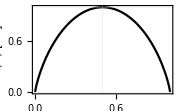

```mathematica
Plot[-(p Log[p]+(1-p)Log[1-p])/Log[2],{p,0,1},PlotStyle->Black,FrameLabel->{"\!\(p\)","\!\(S(X)\) [bit]"},GridLines->{{0.5},{0,1}},ImageSize->180]
```

S(X)=0 when p=0 (X=false for sure) or p=1 (X=true for sure).

S(X) is maximized at p=1/2, where X is most uncertain. The maximum entropy of a binary random variable is 1 bit.

##### The Unit of Entropy

In statistical physics, the thermal entropy (heat-temperature ratio) is defined with an additional factor k_B,

S(X)=-k_B∑_(x∈𝒳) p(x) log p(x).

k_B=1.38065×10^-23J/K is the Boltzmann constant, a conversion constant between the temperature unit and the energy unit.

In natural units (Planck units), k_B=ℏ=c=G=1.

Field of physics | const. | appeared in
Statistical mechanics | k_B | E=k_B T
Quantum mechanics | ℏ | E=ℏ ω
Special relativity | c | E=c p
General relativity | G | E=-G (M m)/r

Fundamental constants are introduced to covert everything to energy.

##### The Epistemological Nature of Entropy

Imagine a box partitioned into two sections. Each half have roughly the same amount of gray balls all bouncing around. [Reference]

```mathematica
DynamicModule[{n=20,a=0.03,run=False,bar=True,col=False,xs,vs,cols,setcol,update},
SeedRandom[0];
xs=Join[#-{0.5,0}&/@RandomReal[{-0.5,0.5},{n/2,2}],#+{0.5,0}&/@RandomReal[{-0.5,0.5},{n/2,2}]];
vs=ReIm@Exp[ⅈ RandomReal[{0,2π},n]];
cols=Table[If[xs[[i,1]]<0,Red,Green],{i,n}];
update[dt_:0.03]:=If[run,Block[{mask,x0s},
Pause[dt];
x0s=xs;
xs=xs +vs dt;
Do[
If[bar,If[(xs[[i,1]]-a)(x0s[[i,1]]-a)<0,xs[[i,1]]=2a-xs[[i,1]];vs[[i,1]]=-vs[[i,1]]];
If[(xs[[i,1]]+a)(x0s[[i,1]]+a)<0,xs[[i,1]]=-2a-xs[[i,1]];vs[[i,1]]=-vs[[i,1]]];];
If[Abs[xs[[i,1]]]>1,xs[[i,1]]=Sign[xs[[i,1]]](2-Abs[xs[[i,1]]]);vs[[i,1]]=-vs[[i,1]]];
If[Abs[xs[[i,2]]]>0.5,xs[[i,2]]=Sign[xs[[i,2]]](1-Abs[xs[[i,2]]]);vs[[i,2]]=-vs[[i,2]]],{i,n}];]];
Deploy@Dynamic[update[];Graphics[{EventHandler[{EdgeForm[Black],White,Rectangle[{-1-a,-0.5-a},{1+a,0.5+a}]},"MouseClicked":>(run=!run)],
EventHandler[{If[col,#1,Gray],Disk[#2,a]},"MouseClicked":>(cols=Table[If[xs[[i,1]]<0,Red,Green],{i,n}];col=!col)]&@@@Thread[{cols,xs}],
EventHandler[{If[bar,Black,Directive[Opacity[0.2],Black,Dashed]],Line[{0,#}&/@{-0.5,0.5}]},"MouseClicked":>(Do[If[Abs[xs[[i,1]]]<=a,xs[[i,1]]=Sign[xs[[i,1]]](Abs[xs[[i,1]]]+a)],{i,n}];bar=!bar)]},ImageSize->180]]]
```

Ruben Verresen. Does entropy depend on observer? Physics StackExchange.

Remove, wait, and re-insert the partition - not much changed - there has been no increase of entropy:

Δ S=0.

However, it turns out we were color blind. The balls are red and green, and initially all red (green) balls are on the left (right). Mixing will increase the entropy by (1 bit for each ball)

Δ S=N log 2.

Which statement is correct?

Both are correct.

Entropy is not a property of the physical system. It depends on what we can (or choose to) measure, and how much details we are able (or willing) to look into.

Information can be used to extract work.

Replace the partition with a semi-permeable membrane that only allows red balls to pass through (i.e., the membrane is not color-blind). It will experience an imbalanced pressure from the green side, known as the osmotic pressure, which can be used to do work.

To us, as color-blind observers, this seems to violate the second law of thermodynamics, that it is impossible to extract work from a maximal entropy system.

However, observing such a work done would force us to reconsider our limitations, and to acknowledge that there must be some underlying difference among the balls, even if we cannot directly perceive it!

### Statistical Inference

#### Maximum Entropy Estimation

Maximum entropy (MaxEnt) estimation is a cornerstone in the realm of statistical inference, offering a principle for estimating probability distributions of random variables. [Reference]

The probability distribution of a random variable X should be assigned to maximize the entropy of X, within the bounds of our existing knowledge about X.

Entropy serves as a metric for our ignorance. By maximizing entropy, we are maximizing our ignorance in a controlled way.

We should be honest about our ignorance. MaxEnt insists that our probabilistic beliefs should be calibrated such that they do not pretend a level of knowledge that exceeds what our evidence or hypotheses justify.

E. T. Jaynes. Why do we Stand on Maximum Entropy. https://bayes.wustl.edu/etj/articles/stand.on.entropy.pdf

Example: uniform distribution

Consider a random variable X with Ω possible values. Without further assumptions, the maximum entropy probability distribution is the uniform (equal probability) distribution:

∀x∈𝒳:p(x)=1/Ω,

which has entropy

S(X)=log Ω.

Prove that the equal probability distribution is maximal entropy.

Objective: variate p(x) to maximize

S(X)=-∑_(x∈𝒳) p(x)log p(x),

subject to the constraint

∑_(x∈𝒳) p(x)=1.

Introduce a Lagrange multiplier λ, the problem becomes to maximize the following objective function (with appropriate choice of λ to be determined later)

ℒ=S(X)+λ (∑_(x∈𝒳) p(x)-1).

Variate ℒ with respect to p(x), the variation must vanish at the maximal point

δℒ/(δ p(x))=- (1+log p(x))+λ=0.

The solution of p(x) is

p(x)=ⅇ^(λ-1).

The Lagrangian multiplier λ must be chosen to satisfy the constraint Eq. (DisplayFormulaNumbered).

∑_(x∈𝒳) p(x)=Ω ⅇ^(λ-1)=1
⇒ ⅇ^(λ-1)=1/Ω.

So the maximal entropy solution is the equal probability distribution

p(x)=1/Ω.

#### Gibbs Distribution

Let X be a random variable, with constraints on the expectation values for a series of functions of x: f_1(x), f_2(x), …

⟨f_a(x)⟩=∑_(x∈𝒳) f_a(x)p(x),

the MaxEnt estimation can be formulated as a constrained optimization problem:

max_(p(x)) S(X)=-∑_(x∈𝒳) p(x)log p(x),
s.t. ∀a:∑_(x∈𝒳) f_a(x)p(x)=⟨f_a(x)⟩.

the optimal probability distribution is the Gibbs distribution [Reference]

p(x)=1/Z[λ]exp(-∑_a λ_a f_a(x)),

Use the Lagrangian multiplier method to show that Eq. (DisplayFormulaNumbered) is the optimal solution of Eq. (DisplayFormulaNumbered).

Objective: variate p(x) to maximize

S(X)=-∑_(x∈𝒳) p(x)log p(x),

subject to the following constraints

∑_(x∈𝒳) p(x)=1,

∑_(x∈𝒳) f_a(x)p(x)=⟨f_a(x)⟩.

Introduce a set of Lagrange multipliers (one for each constraint), construct a new objective function

ℒ=S(X)+λ_0 (∑_(x∈𝒳) p(x)-1)+∑_a λ_a(⟨f_a(x)⟩-∑_(x∈𝒳) f_a(x)p(x)).

Variate ℒ with respect to p(x), and set the variation to zero

δℒ/(δ p(x))=- (1+log p(x))+λ_0-∑_a λ_a f_a(x)=0.

The solution is

p(x)=exp(λ_0-∑_a λ_a f_a(x)-1)=ⅇ^(λ_0-1)exp(-∑_a λ_a f_a(x))

Substitute back to Eq. (DisplayFormulaNumbered) (to normalize the probability),

∑_(x∈𝒳) p(x)=ⅇ^(λ_0-1)∑_(x∈𝒳) exp(-∑_a λ_a f_a(x))=ⅇ^(λ_0-1)Z[λ]=1,

where the partition function Z[λ] has been introduced as

Z[λ]=∑_(x∈𝒳) exp(-∑_a λ_a f_a(x)).

From Eq. (DisplayFormulaNumbered), we have

ⅇ^(λ_0-1)=1/Z[λ],

plugging into Eq. (DisplayFormulaNumbered), we find

p(x)=1/Z[λ]exp(-∑_a λ_a f_a(x))

is properly normalized (λ_0 has been eliminated).

E. T. Jaynes. Information Theory and Statistical Mechanics. https://bayes.wustl.edu/etj/articles/theory.1.pdf

p(x) takes an exponential form, where the exponent is a linear combination of all constraint functions f_a(x) by corresponding Lagrangian multipliers λ_a

p(x)∝exp(-∑_a λ_a f_a(x)).

Z[λ] is called the partition function,

Z[λ]=∑_(x∈𝒳) exp(-∑_a λ_a f_a(x)),

serving as the normalization factor to ensure ∑_(x∈𝒳) p(x)=1.

λ_a are Lagrangian multipliers, which should be determined by solving the corresponding constraint equation

-∂/(∂λ_a)log Z[λ]=⟨f_a(x)⟩.

Derive Eq. (DisplayFormulaNumbered).

Now we need to determine the remaining Lagrange multipliers λ_1,λ_2,…. Note that the following derivative turns out to match ∑_(x∈𝒳) f_a(x)p(x)

-∂/(∂λ_a)log Z[λ]=-1/Z[λ](∂Z[λ])/(∂λ_a)
=-1/Z[λ]∑_(x∈𝒳) ∂/(∂λ_a)exp(-∑_a λ_a f_a(x))
=1/Z[λ]∑_(x∈𝒳) f_a(x)exp(-∑_a λ_a f_a(x))
=∑_(x∈𝒳) f_a(x)p(x).

To satisfy the constraints on expectation values,

∑_(x∈𝒳) f_a(x)p(x)=⟨f_a(x)⟩,

the values of the Lagrange multipliers should be determined by

-∂/(∂λ_a)log Z[λ]=⟨f_a(x)⟩.

The entropy of the optimal distribution Eq. (DisplayFormulaNumbered) is

S(X)=log Z[λ]+∑_a λ_a⟨f_a(x)⟩
=(1-∑_a ∂/(∂log λ_a))log Z[λ],

which has been maximal under the constraints of ⟨f_a(x)⟩.

Derive Eq. (DisplayFormulaNumbered).

Given the solution Eq. (DisplayFormulaNumbered) of the probability, the entropy can be calculated

S(X)=-∑_(x∈𝒳) p(x)log p(x)
=-∑_(x∈𝒳) p(x)(-log Z[λ]-∑_a λ_a f_a(x))
=log Z[λ]∑_(x∈𝒳) p(x)+∑_a λ_a∑_(x∈𝒳) f_a(x)p(x)
=log Z[λ]+∑_a λ_a⟨f_a(x)⟩.

Consider a six-sided dice (with face numbered 1 to 6). However, the dice may not be fair. You are given the knowledge that the expectation value of a roll is 4.5. Your task is to determine the probability distribution of outcome numbers using the maximal entropy estimation. 
(i) Define the random variable in the problem. Given its expectation value, formulate the constraint for the probabilities.
(ii) Use the maximal entropy principle to set up the constrained optimization problem. Solve the problem by the Lagrangian multiplier method or by a computer program. 
(iii) Make a table of the probability distributions you found (numerical values), like the following:
x | 1 | 2 | 3 | 4 | 5 | 6
p(x) | □ | □ | □ | □ | □ | □.

## Statistical Ensembles

### Microcanonical Ensemble

#### Probability Distribution

The microcanonical ensemble describes isolated (closed) systems, with fixed energy E and number of particles N.

```mathematica
Block[{ar=0.618,d=0.15,lt=0.5,a=0.06,n=10},
SeedRandom[4];Graphics[{{EdgeForm[Black],{HatchFilling[],Rectangle[{-ar-d,-1-d},{ar+d,1+d}]},{Lighter[Red,lt],Rectangle[{-ar,-1},{ar,1}]}},{Disk[#,a]&/@Thread[{RandomReal[{-ar+a,ar-a},n],RandomReal[{-1+a,1-a},n]}]},
Text[Style["\!\(E,N\)",Background->Lighter[Red,lt]],{ar,-1},{1.1,-1}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->140]]
```

-Graphics-

All accessible microstates x∈𝒳_(E,N) of the system have the same energy E and particle number N. The ensemble of all such systems belongs to the same macrostate labeled by (E,N).

Without further constraints, the MaxEnt estimation asserts that the probability distribution is uniform, i.e., every microstate is equally likely

p(x)=1/(Ω(E,N)),

where

Ω(E,N) is the number of microstates in 𝒳_(E,N) (the set of microstates with energy E and particle number N),

Ω(E,N)=∑_(x∈𝒳_(E,N)) 1.

In microcanonical ensemble, Ω(E,N) serves the role of the partition function.

#### Thermodynamics

The entropy is given by [recall the entropy formula Eq. (DisplayFormulaNumbered)]

S(E,N)=log Ω(E,N).

The entropy function enables us to define temperature T and chemical potential μ through its derivatives, [accept these definitions as historical conventions for now]

((∂S)/(∂E))_N=1/T,
((∂S)/(∂N))_E=-μ/T.

In differential form,

ⅆS=1/T ⅆE-μ/T ⅆN,

which can be written in a more familiar form as the thermodynamic identity for energy

ⅆE=TⅆS+μ ⅆN.

This is also known as the first law of thermodynamics, which states that the energy change ⅆE is a sum of heat TⅆS and work  μⅆN.

The conjugate pair (μ,N) can be replace by other pairs in other thermodynamic problems, but the underlying principles are the same. [See the section Conjugate Pairs of Variables for more examples.]

##### Equilibrium Condition

Why are temperature and chemical potential defined in this way (as in Eq. (DisplayFormulaNumbered))? This has to do with what we mean by thermal and chemical equilibrium.

Equilibrium: probability distribution does not evolve in time.

Consider two initially isolated systems.

The probability to observe them in microstates (x_1,x_2) is

p_0(x_1,x_2)=p(x_1)p(x_2).

Imaging bringing the two systems in contact for some time t. They jointly evolve into new microstates:

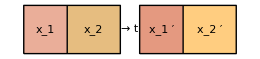

```mathematica
Block[{r=0.45,h=0.5,d=0.6,box},
box[lt_:0,p_:""]:={{Lighter[Lighter[Red,lt],0.5],Rectangle[{0,0},{r,h}],Lighter[Darker[Orange,lt],0.5],Rectangle[{r,0},{1,h}]},{Line[{{0,0},{0,h},{1,h},{1,0},{0,0}}],Line[{{r,0},{r,h}}],
Text["\!\(x\_1"<>p<>"\)",{r/2,h/2},{0,0}],
Text["\!\(x\_2"<>p<>"\)",{(r+1)/2,h/2},{0,0}]}};
Graphics[{Translate[box[0.2,""],{-d,0}],Text["\!\(→\&t\)",{0.5,h/2},{0,0}],Translate[box[0,"\%′"],{d,0}]},ImageSize->260]]
```

Assuming the time evolution is deterministic, the probability to observe (x'_1,x'_2) after the contact is

p_t(x'_1,x'_2)=p_0(x_1,x_2)=p(x_1)p(x_2).

If the two systems were in equilibrium, their joint probability distribution should be time independent, meaning

p_t(x'_1,x'_2)=p_0(x'_1,x'_2)=p(x'_1)p(x'_2).

So the equilibrium condition (at the probability level) is

p(x_1)p(x_2)=p(x'_1)p(x'_2),

for any (x'_1,x'_2) related to (x_1,x_2) by time evolution.

What is its implication for microcanonical ensembles?

For microcanonical ensembles, p(x) only depends on the energy E and particle number N of the microstate x

p(x)=1/(Ω(E,N)).

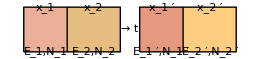

```mathematica
Block[{r=0.45,h=0.5,d=0.6,box},
box[lt_:0,p_:""]:={{Lighter[Lighter[Red,lt],0.5],Rectangle[{0,0},{r,h}],Lighter[Darker[Orange,lt],0.5],Rectangle[{r,0},{1,h}]},{Line[{{0,0},{0,h},{1,h},{1,0},{0,0}}],Line[{{r,0},{r,h}}],
Text["\!\(x\_1"<>p<>"\)",{r/2,h},{0,1}],
Text["\!\(x\_2"<>p<>"\)",{(r+1)/2,h},{0,1}],Text["\!\(E\_1"<>p<>",N\_1"<>p<>"\)",{r/2,0},{0,-1}],
Text["\!\(E\_2"<>p<>",N\_2"<>p<>"\)",{(r+1)/2,0},{0,-1}]}};
Graphics[{Translate[box[0.2,""],{-d,0}],Text["\!\(→\&t\)",{0.5,h/2},{0,0}],Translate[box[0,"\%′"],{d,0}]},ImageSize->260]]
```

The equilibrium condition Eq. (DisplayFormulaNumbered) implies

1/(Ω(E_1,N_1))1/(Ω(E_2,N_2))=1/(Ω(E'_1,N'_1))1/(Ω(E'_2,N'_2)),

Taking logarithm on both side, noting S=log Ω, Eq. (DisplayFormulaNumbered) becomes

S(E_1,N_1)+S(E_2,N_2)=S(E'_1,N'_1)+S(E'_2,N'_2),

meaning that the total entropy will not evolve in time, if two systems have reached equilibrium. Note that the energy and particle number are also time invariant by conservation laws,

E_1+E_2=E'_1+E'_2,
N_1+N_2=N'_1+N'_2.

These can be summarized in differential forms as (under infinitesimal evolution of time ⅆt)

ⅆ E_1+ⅆ E_2=0,
ⅆ N_1+ⅆ N_2=0,
ⅆS(E_1,N_1)+ⅆS(E_2,N_2)
=((∂S)/(∂E_1))_N_1 ⅆ E_1+((∂S)/(∂N_1))_E_1 ⅆ N_1+((∂S)/(∂E_2))_N_2 ⅆ E_2+((∂S)/(∂N_2))_E_2 ⅆ N_2
=0.

Result in two equilibrium conditions (at the thermodynamic level)

Derive the following two equilibrium conditions from Eq. (DisplayFormulaNumbered).

Using the first two equations of Eq. (DisplayFormulaNumbered)

ⅆ E_1+ⅆ E_2=0⇒ⅆ E_2=-ⅆ E_1,
ⅆ N_1+ⅆ N_2=0⇒ⅆ N_2=-ⅆ N_1,

we can eliminate ⅆ E_2 and ⅆ N_2 in the last equation of Eq. (DisplayFormulaNumbered), such that

((∂S)/(∂E_1))_N_1 ⅆ E_1+((∂S)/(∂N_1))_E_1 ⅆ N_1-((∂S)/(∂E_2))_N_2 ⅆ E_1-((∂S)/(∂N_2))_E_2 ⅆ N_1
=(((∂S)/(∂E_1))_N_1-((∂S)/(∂E_2))_N_2)ⅆ E_1+(((∂S)/(∂N_1))_E_1-((∂S)/(∂N_2))_E_2)ⅆ N_1
=0.

Without specifying the microscopic process, ⅆ E_1 and ⅆ N_1 are arbitrary. For the above equation to hold, we must require

((∂S)/(∂E_1))_N_1-((∂S)/(∂E_2))_N_2=0,
((∂S)/(∂N_1))_E_1-((∂S)/(∂N_2))_E_2=0.

The thermal equilibrium condition

1/T_1=((∂S)/(∂E_1))_N_1=((∂S)/(∂E_2))_N_2=1/T_2,

or equivalently

T_1=T_2,

which defines what should be called temperature.

The chemical equilibrium condition

-μ_1/T_1=((∂S)/(∂N_1))_E_1=((∂S)/(∂N_2))_E_2=-μ_2/T_2,

or equivalently (assuming T_1=T_2 is already achieved)

μ_1=μ_2,

which defines what should be called chemical potential.

### Canonical Ensemble

#### Probability Distribution

The canonical ensemble describes isothermal systems (thermally open and particle-wise closed), in thermal equilibrium with a heat bath, with fixed temperature T and number of particles N.

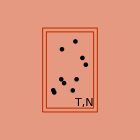

```mathematica
Block[{ar=0.618,d=0.1,lt=0.5,a=0.06,n=10},
SeedRandom[4];Graphics[{{EdgeForm[Red],{Lighter[Red,lt],Rectangle[{-ar-d,-1-d},{ar+d,1+d}]},{Lighter[Red,lt],Rectangle[{-ar,-1},{ar,1}]}},{Disk[#,a]&/@Thread[{RandomReal[{-ar+a,ar-a},n],RandomReal[{-1+a,1-a},n]}]},
Text[Style["\!\(T,N\)",Background->Lighter[Red,lt]],{ar,-1},{1.1,-1}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Background->Lighter[Red,lt],ImageSize->140]]
```

Microstates x∈𝒳_N of the system still have the same particle number N, but can take all different energies.

An energy function E(x) is therefore introduced to evaluate the energy associated with each state x.

One can still talk about the energy expectation value for the ensemble

E=⟨E(x)⟩=∑_(x∈𝒳_N) E(x)p(x).

Given temperature T, the ensemble is expected to have an energy expectation value ⟨E(x)⟩ that matches the macroscopic energy E.

Given the energy constraint ⟨E(x)⟩=E, the MaxEnt estimation asserts that the probability distribution should be [recall Eq. (DisplayFormulaNumbered)]

p(x)=1/(Z(β,N))ⅇ^(-β E(x)),

where

The partition function Z(β,N) is given by

Z(β,N)=∑_(x∈𝒳_N) ⅇ^(-β E(x)).

Originally introduced as a Lagrangian multiplier,  β is found to be related to the temperature T by (assuming k_B=1)

β=1/T,

so  β is also called the inverse temperature.

##### Lagrangian Multipliers

The Lagrangian multiplier β was introduced to enforce the energy constraint ⟨E(x)⟩=E, so it should be determined by solving the constraint equation, according to Eq. (DisplayFormulaNumbered), -∂_λ_a log Z[λ]=⟨f_a⟩,

E=-((∂log Z)/(∂β))_N.

On the other hand, Eq. (DisplayFormulaNumbered), S=log Z+∑_a λ_a⟨f_a⟩, tells us how to compute entropy,

S=log Z+β E.

Take the total derivative on both sides,

ⅆS=β ⅆE+((∂log Z)/(∂N))_β ⅆN.

Derive Eq. (DisplayFormulaNumbered) using Eq. (DisplayFormulaNumbered).

For canonical ensemble, β and N are independent thermodynamic variables,

ⅆS=ⅆ(log Z)+ⅆ(β E)
=((∂log Z)/(∂β))_N ⅆβ+((∂log Z)/(∂N))_β ⅆN+β ⅆE+Eⅆβ
=^(Eq. (DisplayFormulaNumbered))-Eⅆβ+((∂log Z)/(∂N))_β ⅆN+β ⅆE+Eⅆβ
=β ⅆE+((∂log Z)/(∂N))_β ⅆN.

Compared with Eq. (DisplayFormulaNumbered), which defines temperature and chemical potential,

ⅆS=1/T ⅆE-μ/T ⅆN,

one concludes that

β=1/T,
μ=-T ((∂log Z)/(∂N))_β=-T ((∂log Z)/(∂N))_T.

#### Thermodynamics

The logarithm of partition function log Z defines the (Helmholtz) free energy,

F(T,N)=-T log Z(1/T,N).

The free energy enables us to compute:

Entropy

S=-((∂F)/(∂T))_N,

Derive Eq. (DisplayFormulaNumbered).

Starting from the entropy formula Eq. (DisplayFormulaNumbered),

S=(1-∂/(∂log β))log Z
=(1+∂/(∂log T))log Z.

In this step, we have used the following facts:

β=1/T
⇒log β=-log T
⇒ⅆ(log β)=-ⅆ(log T)
⇒∂/(∂log β)=-∂/(∂ log T).

So the entropy can be expanded as

S=log Z+(∂log Z)/(∂log T)
=log Z+T∂/(∂T)log Z
=∂/(∂T)(T log Z)
=-(∂F)/(∂T).

Through out the process, N is held fixed.

Chemical potential

μ=((∂F)/(∂N))_T.

Derive Eq. (DisplayFormulaNumbered).

From Eq. (DisplayFormulaNumbered),

μ=-T ((∂log Z)/(∂N))_T.

By definition F=-T log Z, so

μ=((∂(-T log Z))/(∂N))_T=((∂F)/(∂N))_T.

In differential form,

ⅆF=-S ⅆT+μⅆN.

This is the thermodynamic identity for free energy.

Moreover, the free energy is related to the energy by

F=E-T S.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

By Eq. (DisplayFormulaNumbered),

S=log Z+β E 
⇒log Z=S-β E=S-E/T.

By definition,

F=-T log Z=-T(S-E/T)=E-T S.

Conversely, the energy can be reconstructed from the free energy

E=F-(T((∂F)/(∂T)))_N.

Statistical physics of a qubit. A qubit is a system with two states (labeled by x=0,1): a ground state of energy E(0)=0, and an excited state of energy E(1)=ϵ (where ϵ>0). Suppose the qubit is in thermal equilibrium with a heat bath at temperature T. (The number of particles can be treated as N=1, and is not relevant to the problem.)
(i) Calculate the partition function Z in terms of ϵ and T=1/β. 
(ii) Derive the expression for the probabilities p(x) of finding the qubit in the ground state (x=0) and the excited state (x=1), respectively.
Let us compute the entropy S in two different ways: 
(iii) From the partition function Z, calculate the free energy F=-T log Z, and then obtain S=-∂F/∂T. 
(iv) From the probability distribution p(x), calculate the entropy by definition S=-∑_x p(x)log p(x). 
Compare the results obtained in (iii) and (iv) and show that they are the same.
(v) Plot the entropy S as a function of temperature T (taking ϵ=1 as the energy unit), discuss the behavior at low and high temperatures.

### Grand Canonical Ensemble

#### Probability Distribution

The grand canonical ensemble describes open systems, in thermal and chemical equilibrium with a reservoir, at fixed temperature T and chemical potential μ.

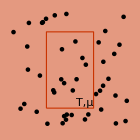

```mathematica
Block[{ar=0.618,d=0.15,lt=0.5,a=0.06,n=10},
SeedRandom[4];Graphics[{{EdgeForm[Directive[Red,Dashed]],Lighter[Red,lt],Rectangle[{-ar,-1},{ar,1}]},{Disk[#,a]&/@Thread[{RandomReal[{-ar+a,ar-a},n],RandomReal[{-1+a,1-a},n]}]},
{Disk[#,a]&/@Cases[RandomReal[{-1.5,1.5},{50,2}],{x_,y_}/;Abs[x]>ar+a||Abs[y]>1+a]},
Text[Style["\!\(T,μ\)",Background->Lighter[Red,lt]],{ar,-1},{1.1,-1}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Background->Lighter[Red,lt],ImageSize->140]]
```

Microstates x∈𝒳 can take all possible states of different energies and particle numbers.

To evaluate the energy and particle number associated with a particular microstate x, the energy function E(x) and the particle number function N(x) are introduced respectively.

The energy E and particle number N of the macrostate refers to their expectation values in grand canonical ensemble

E=⟨E(x)⟩=∑_(x∈𝒳) E(x)p(x),
N=⟨N(x)⟩=∑_(x∈𝒳) N(x)p(x).

Given the energy constraint ⟨E(x)⟩=E and the particle number constraint ⟨N(x)⟩=N, the MaxEnt estimation asserts that the probability distribution should be [recall Eq. (DisplayFormulaNumbered)]

p(x)=1/(ℨ(β,μ))ⅇ^(-β (E(x)-μ N(x))),

where

The (grand) partition function ℨ(β,μ) is given by

ℨ(β,μ)=∑_(x∈𝒳) ⅇ^(-β (E(x)-μ N(x))).

The Lagrangian multipliers are parameterized by the inverse temperature β=1/T and the chemical potential μ.

##### Lagrangian Multipliers

To figure out the physical meaning of Lagrangian multipliers, first rewrite the partition function Eq. (DisplayFormulaNumbered) as

ℨ(β,-γ/β)=∑_(x∈𝒳) ⅇ^(-β E(x)-γ N(x)),

such that β and γ can be treated as independent Lagrangian multipliers. According to Eq. (DisplayFormulaNumbered), -∂_λ_a log Z[λ]=⟨f_a⟩, their corresponding constraint equations are

E=-((∂log ℨ)/(∂β))_γ,
N=-((∂log ℨ)/(∂γ))_β,

On the other hand, Eq. (DisplayFormulaNumbered), S=log Z+∑_a λ_a⟨f_a⟩, tells us how to compute entropy,

S=log ℨ+β E+γ N.

Take the total derivative on both sides,

ⅆS=βⅆE+γⅆN.

Derive Eq. (DisplayFormulaNumbered) using Eq. (DisplayFormulaNumbered).

ⅆS=ⅆ(log ℨ)+ⅆ(β E)+ⅆ(γ N)
=((∂log ℨ)/(∂β))_γ ⅆβ+((∂log ℨ)/(∂γ))_β ⅆγ+βⅆE+Eⅆβ+γⅆN+Nⅆγ
=^(Eq. (DisplayFormulaNumbered))-Eⅆβ-Nⅆγ+βⅆE+Eⅆβ+γⅆN+Nⅆγ
=βⅆE+γⅆN.

Compared with Eq. (DisplayFormulaNumbered), which defines temperature and chemical potential,

ⅆS=1/T ⅆE-μ/T ⅆN,

one concludes that

β=1/T,
γ=-μ/T,

which justify the parametrization of Lagrangian multipliers in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

#### Thermodynamics

The logarithm of (grand) partition function log ℨ defines the (grand) free energy,

𝔉(T,μ)=-T log ℨ(1/T,μ).

Some textbook defines a similar concept, call the “grand potential”: Φ(T,μ)=-𝔉(T,μ).

The (grand) free energy enables us to compute:

Entropy

S=-((∂𝔉)/(∂T))_μ,

Derive Eq. (DisplayFormulaNumbered).

Rewrite the partition function as

ℨ(β,-γ/β)=∑_(x∈𝒳) ⅇ^(-β E(x)-γ N(x)),

with γ=-β μ. In this form, β and γ are independent Lagrangian multipliers. Starting from the entropy formula Eq. (DisplayFormulaNumbered),

S=log ℨ-((∂log ℨ)/(∂log β))_γ-((∂log ℨ)/(∂log γ))_β.

To simplify, note that

{ | β=1/T,
γ=-μ/T,
⇒{ | log β=-log T,
log γ=log(-μ)-log T,
⇒{ | ⅆ(log β)=-ⅆ(log T),
ⅆ(log γ)=ⅆ(log(-μ))-ⅆ(log T).

If the μ is held fixed (i.e. ⅆμ=0), log β and log γ both variates with log T as

{ | ⅆ(log β)=-ⅆ(log T),
ⅆ(log γ)=-ⅆ(log T).

Therefore,

((∂log ℨ)/(∂log T))_μ=-((∂log ℨ)/(∂log β))_γ-((∂log ℨ)/(∂log γ))_β,

so the entropy can be expanded as

S=log ℨ+((∂log ℨ)/(∂log T))_μ
=log ℨ+(T((∂log ℨ)/(∂T)))_μ
=((∂(T log ℨ))/(∂T))_μ
=-((∂𝔉)/(∂T))_μ.

Particle number

N=-((∂𝔉)/(∂μ))_T,

Derive Eq. (DisplayFormulaNumbered).

From Eq. (DisplayFormulaNumbered),

N=-((∂log ℨ)/(∂γ))_β.

Given that γ=-β μ, so ⅆγ=-β ⅆμ when β is held fixed. Thus the above formula can be rewritten as

N=-((∂log ℨ)/(-β∂μ))_β
=1/β((∂log ℨ)/(∂μ))_β.

Further using β=1/T,

N=(T((∂log ℨ)/(∂μ)))_T
=-((∂(-T log ℨ))/(∂μ))_T
=-((∂𝔉)/(∂μ))_T.

In differential form,

ⅆ𝔉=-SⅆT-Nⅆμ.

This is the thermodynamic identity for (grand) free energy.

Moreover, the (grand) free energy is related to the energy by

𝔉=E-T S-μ N.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

By Eq. (DisplayFormulaNumbered),

S=log ℨ+β E+γ N
⇒log ℨ=S-β E-γ N=S-E/T+(μ N)/T.

By definition,

𝔉=-T log ℨ=-T(S-E/T+(μ N)/T)
=E-T S-μ N.

Conversely, the energy can be reconstructed from the (grand) free energy.

E=𝔉-(T((∂𝔉)/(∂T)))_μ-(μ((∂𝔉)/(∂μ)))_T.

### Summary

#### Statistical Ensembles

Comparison of the three primary statistical ensembles:

Ensemble | Microcanonical |   | Canonical |   | Grand Canonical
Microstates | 𝒳_(E,N) | ⊆ | 𝒳_N | ⊆ | 𝒳
Macrostate | (E,N) |   | (T,N) |   | (T,μ)
Probability | p=1/Ω |   | p=1/Z ⅇ^(-β E) |   | p=1/ℨ ⅇ^(-β (E-μ N))
Partition function | Ω=∑1 |   | Z=∑ⅇ^(-β E) |   | ℨ=∑ⅇ^(-β (E-μ N))
Free energy | none |   | F=-T log Z |   | 𝔉=-T log ℨ
Entropy | S=log Ω |   | S=-((∂F)/(∂T))_N |   | S=-((∂𝔉)/(∂T))_μ
Energy | E |   | E=F+T S |   | E=𝔉+T S+μ N
Particle number | N |   | N |   | N=-((∂𝔉)/(∂μ))_T
Temperature | T=((∂E)/(∂S))_N |   | T |   | T
Chemical potential | μ= ((∂E)/(∂N))_S |   |  μ=((∂F)/(∂N))_T |   | μ
Thermodynamics | ⅆE=TⅆS+μ ⅆN |   | ⅆF=-S ⅆT+μⅆN |   | ⅆ𝔉=-SⅆT-Nⅆμ

#### Conjugate Pair of Variables

In thermodynamics, a conjugate pair of variables is a pair of

Intensive variable (like T, μ) to be balanced at equilibrium,

Extensive variable (like E, N) to be transferred in order to reach the equilibrium,

such that they multiplies to an energy unit.

We have only focused on (T,S) and (μ,N) pairs in the above discussion. However, the principle of statistical mechanics can be applied to much broader systems:

Process/System | Conjugate pair of variables |  | Contribution
 | Intensive variable | Extensive variable | to energy (ⅆE)
Heat transfer | Temperature (T) | Entropy (S) | +TⅆS
Particle transfer | Chemical potential (μ) | Particle number (N) | +μⅆN
Charge transfer | Electric potential (ℰ) | Charge (Q) | +ℰⅆQ
Gas, Liquid | Pressure (P) | Volume (V) | -PⅆV
Membrane | Surface tension (γ) | Area (A) | -γⅆA
Elastic material | Stree tensor (σ) | Strain tensor (ϵ) | +Tr σⅆϵ
Dielectric material | Electric field (D) | Electric polarization (P) | -1/εD·ⅆP
Magnetic material | Magnetic field (B) | Magnetization (M) | -B·ⅆM
Rotating galaxy | Angular velocity (ω) | Angular momentum (L) | +ωⅆL

This flexibility allows for a comprehensive modeling of a wide range of physical phenomena.

For example, we want to model a system of

Gas (-PⅆV),

with

Heat transfer (+TⅆS),

Particle transfer (+μⅆN).

The thermodynamics is described by

ⅆE=-PⅆV+TⅆS+μⅆN,

or, in terms of free energies,

ⅆF=-PⅆV-S ⅆT+μⅆN,
ⅆ𝔉=-PⅆV-SⅆT-Nⅆμ.

This enables us to write done thermodynamic identities, such as

P=-((∂𝔉)/(∂V))_(T,μ),
S=-((∂𝔉)/(∂T))_(V,μ),
N=-((∂𝔉)/(∂μ))_(V,T).